Find the exact potential for a uniform density sphere of radius R with Yukawa force, rather than point charge approx.  First need to solve (∇^2 -m_ϕ^2)V=-k ρ_Twhere ρ_Tis the neutron density of the target, and k is some constant to give the same units as Gordan’s note:

```mathematica
DSolve[f''[r]+2f'[r]/r -Subscript[m, ϕ]^2 f[r] == -k Subscript[ρ, T], f[r],r]
```

{{f[r]→(ⅇ^(-r m_ϕ) C[1])/r+(ⅇ^(r m_ϕ) C[2])/(2 r m_ϕ)+(k ρ_T)/m_ϕ^2}}

Outside we have ρ_T=0 and need the solution to go to zero at infinity:

```mathematica
fout[r_] = (A ⅇ^(-Subscript[m, ϕ]r))/r;
```

Inside we have non-zero ρ_T and require the solution doesn’t diverge at r->0:

```mathematica
fin[r_]= (k Subscript[ρ, T])/Subscript[m, ϕ]^2+B Sinh[Subscript[m, ϕ] r]/(Subscript[m, ϕ] r);
```

Additional boundary conditions are continuity of potential and gradient at surface:

```mathematica
rr=Solve[{fin[R] == fout[R], fin'[R]==fout'[R]}, {A,B}]
```

{{A→(ⅇ^(R m_ϕ) k (-Sinh[R m_ϕ]+R Cosh[R m_ϕ] m_ϕ) ρ_T)/((Cosh[R m_ϕ]+Sinh[R m_ϕ]) m_ϕ^3),B→-(k Csch[R m_ϕ] (1+R m_ϕ) ρ_T)/((1+Coth[R m_ϕ]) m_ϕ^2)}}

```mathematica
FullSimplify[fout[r]/.rr]
```

{(ⅇ^(-r m_ϕ) k (-Sinh[R m_ϕ]+R Cosh[R m_ϕ] m_ϕ) ρ_T)/(r m_ϕ^3)}

```mathematica
FullSimplify[fin[r]/.rr]
```

{(k (m_ϕ-(Csch[R m_ϕ] Sinh[r m_ϕ] (1+R m_ϕ))/(r (1+Coth[R m_ϕ]))) ρ_T)/m_ϕ^3}

Now fill in the value for k to match Gordan’s note.  Overall scale factor for potential given by α -- set to 1 for now for plotting, but in general α = (N_T N_χ y_T y_χ)/(4π):

```mathematica
α =1;
```

Potential outside sphere (from above, rewriting a bit nicer):

```mathematica
Subscript[V, out] = (3α)/(Subscript[m, ϕ] R)^3(Subscript[m, ϕ] R Cosh[Subscript[m, ϕ] R] - Sinh[Subscript[m, ϕ] R])Exp[-Subscript[m, ϕ]r]/r;
```

Check limit is correct for a point mass:

```mathematica
Subscript[V, 0] = Limit[Subscript[V, out], R->0]
```

ⅇ^(-r m_ϕ)/r

Potential inside the sphere (from above, rewriting a bit nicer):

```mathematica
Subscript[V, in] = (3α)/(Subscript[m, ϕ] R)^3(Subscript[m, ϕ]-(1 + Subscript[m, ϕ] R)/(r(1+Coth[Subscript[m, ϕ] R ]))(Sinh[Subscript[m, ϕ] r ]/Sinh[Subscript[m, ϕ] R]));
```

```mathematica
Subscript[V, tot] = Piecewise[{{Subscript[V, out], r>R},{Subscript[V, in],r≤R}}];
```

Plot for a few different parameters:

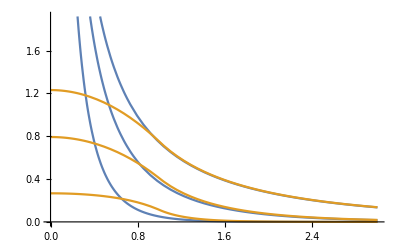

```mathematica
Plot[{Subscript[V, 0]/.{Subscript[m, ϕ]->{0.3,1,3}},Subscript[V, tot]/.{R->1,Subscript[m, ϕ]->{0.3,1,3}}},{r,0,3}]
```

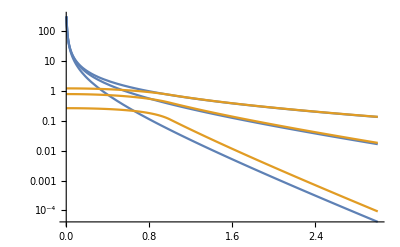

```mathematica
LogPlot[{Subscript[V, 0]/.{Subscript[m, ϕ]->{0.3,1,3}},Subscript[V, tot]/.{R->1,Subscript[m, ϕ]->{0.3,1,3}}},{r,0,3}]
```